```mathematica
α=I ω/v;
s11 = (z-z0)/(z+z0);
z = z0 Coth[α l]-I/(ω C);
```

```mathematica
s11
```

(-z0-ⅈ/(C ω)-ⅈ z0 Cot[(l ω)/v])/(z0-ⅈ/(C ω)-ⅈ z0 Cot[(l ω)/v])

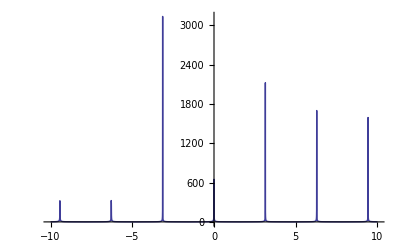

```mathematica
Plot[Abs[Cot[x]],{x,-10,10},PlotRange->Full]
```

```mathematica
wp = {z0 -> 50,v->1,l->1,C->0.001,ω->2π f};
```

```mathematica
phasein = Arg[s11/.wp]
```

Arg[(-50-(0.+159.155 ⅈ)/f-50 ⅈ Cot[2 f π])/(50-(0.+159.155 ⅈ)/f-50 ⅈ Cot[2 f π])]

```mathematica
Block[{freqs = Range[0.2,1.2,0.001]},Export[NotebookDirectory[]<>"cpw_lambda_over_4_phase_and_abs_example.csv",Transpose[{freqs,Map[Evaluate[phasein /.{f->#}]&,freqs],Map[Evaluate[Abs[z] /. wp /.{f->#}]&,freqs]}]]];
```

```mathematica
NotebookDirectory[]
```

E:\cygwin\home\adewes\thesis\material\mathematica\

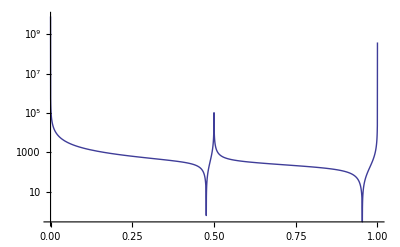

```mathematica
LogPlot[Abs[z /. wp],{f,0,1},PlotRange->Full]
```

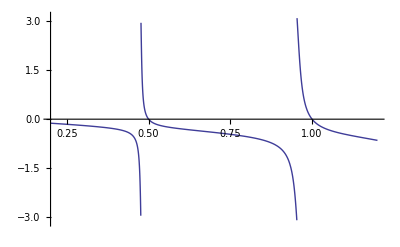

```mathematica
Plot[phasein,{f,0.2,1.2},PlotRange->{-π,π},AxesLabel->{}]
```

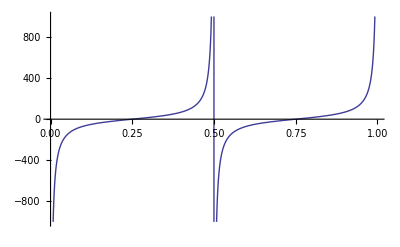

```mathematica
Plot[Im[z0 Coth[α l] /.wp],{f,0,1},PlotRange->{-1000,1000}]
```

```mathematica
Series[1/Cot[x],{x,π,3}]
```

(x-π)+1/3 (x-π)^3+O[x-π]^4